## Nucleation Analysis (Multi - stranded)

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

PartitionFunctionFILE="PartitionFunction_0_0.out";
dPartitionFunctionFILE="dPartitionFunction_0_0.out";
FreeEnergyFILE="FreeEnergy_0_0.out";
dFreeEnergyFILE="dFreeEnergy_0_0.out";
PotentialDataFILE="POTENTIAL_DATA";
ParametersFILE="Parameters";

CollagenPATH="collagen/results/";
OtherHarmonic1PATH="collagen_anhar1/results/";
OtherHarmonic2PATH="collagen_anhar2/results/";

FrameBox["Numerical Parameters - Harmonic"] // DisplayForm
PartitionFunctionCollagen=Import[CollagenPATH <>PartitionFunctionFILE,"Table"];
dPartitionFunctionCollagen=Import[CollagenPATH <>dPartitionFunctionFILE,"Table"];
FreeEnergyCollagen=Import[CollagenPATH <>FreeEnergyFILE,"Table"];
dFreeEnergyCollagen=Import[CollagenPATH <>dFreeEnergyFILE,"Table"];
PotentialCollagen=Import[CollagenPATH <> PotentialDataFILE,"Table"];
ParametersCollagen=Import[CollagenPATH <>ParametersFILE,"Grid"]

FrameBox["Numerical Parameters - Anharmonic 1"] // DisplayForm
PartitionFunctionCollagenAnhar1=Import[OtherHarmonic1PATH<>PartitionFunctionFILE,"Table"];
dPartitionFunctionCollagenAnhar1=Import[OtherHarmonic1PATH<>dPartitionFunctionFILE,"Table"];
FreeEnergyCollagenAnhar1=Import[OtherHarmonic1PATH<>FreeEnergyFILE,"Table"];
dFreeEnergyCollagenAnhar1=Import[OtherHarmonic1PATH<>dFreeEnergyFILE,"Table"];
PotentialCollagenAnhar1=Import[OtherHarmonic1PATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnhar1=Import[OtherHarmonic1PATH<>ParametersFILE,"Grid"]

FrameBox["Numerical Parameters - Anharmonic 2"] // DisplayForm
PartitionFunctionCollagenAnhar2=Import[OtherHarmonic2PATH<>PartitionFunctionFILE,"Table"];
dPartitionFunctionCollagenAnhar2=Import[OtherHarmonic2PATH<>dPartitionFunctionFILE,"Table"];
FreeEnergyCollagenAnhar2=Import[OtherHarmonic2PATH<>FreeEnergyFILE,"Table"];
dFreeEnergyCollagenAnhar2=Import[OtherHarmonic2PATH<>dFreeEnergyFILE,"Table"];
PotentialCollagenAnhar2=Import[OtherHarmonic2PATH<>PotentialDataFILE,"Table"];
ParametersCollagenAnhar2=Import[OtherHarmonic2PATH<>ParametersFILE,"Grid"]

L=IntegerPart[ParametersCollagen[[1,2]][[2]]];
m=IntegerPart[ParametersCollagen[[1,3]][[2]]];
n=IntegerPart[ParametersCollagen[[1,4]][[2]]];
kappa=IntegerPart[ParametersCollagen[[1,5]][[2]]];
sigma=IntegerPart[ParametersCollagen[[1,6]][[2]]];

potentialData={PotentialCollagen,PotentialCollagenAnhar1,PotentialCollagenAnhar2};
FreeEnergyData = {FreeEnergyCollagen,FreeEnergyCollagenAnhar1,FreeEnergyCollagenAnhar2};
dFreeEnergyData={dFreeEnergyCollagen,dFreeEnergyCollagenAnhar1,dFreeEnergyCollagenAnhar2};

fsAxesLabel=24;
fs2=18;
fs3=16;

Needs["PlotLegends`"]
```

C:\Users\Hemant\Desktop\CORRECTIONSv1\Results\Collagen\various_potentials\collagen_sim_results

Numerical Parameters - Harmonic

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Numerical Parameters - Anharmonic 1

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Numerical Parameters - Anharmonic 2

| 
L: | 6.
m: | 24
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.12
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Potential Analysis

```mathematica
FrameBox["Potential Analysis"] // DisplayForm

potentialDataPlotAll=ListLinePlot[
{
PotentialCollagen,
PotentialCollagenAnhar1,
PotentialCollagenAnhar2
},
PlotRange->{{-L/2,L/2},{0,4}},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["η_i",FontSize->fsAxesLabel],
Style["V(η_i)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,RGBColor[50/255,137/255,170/255]},
{Thick,Dashed,Red},
{Thick,Dashed,Orange}
},
PlotLegend->{
Style["Harmonic",FontSize->fs3],
Style["Hard-Soft",FontSize->fs3],
Style["Soft-Hard",FontSize->fs3]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.55,0.25},
LegendPosition->{-0.7,-0.1}
]

Export["./col_pe_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",potentialDataPlotAll];
```

Potential Analysis

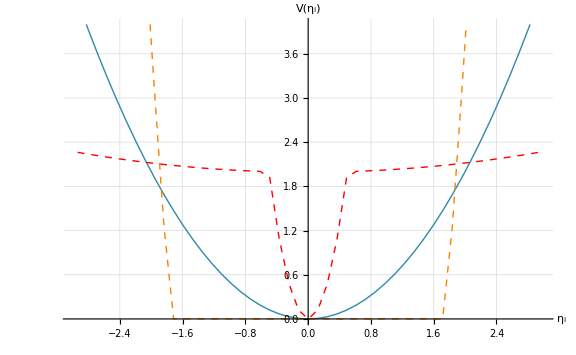

Free Energy Analysis

Free Energy Analysis

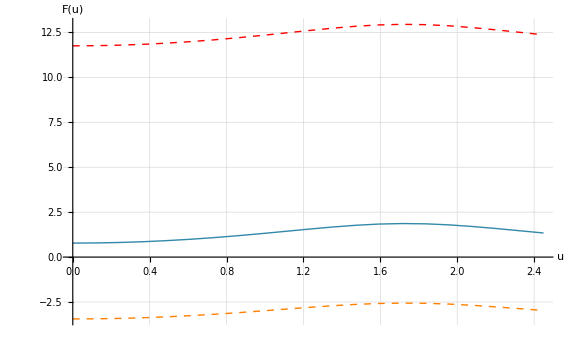

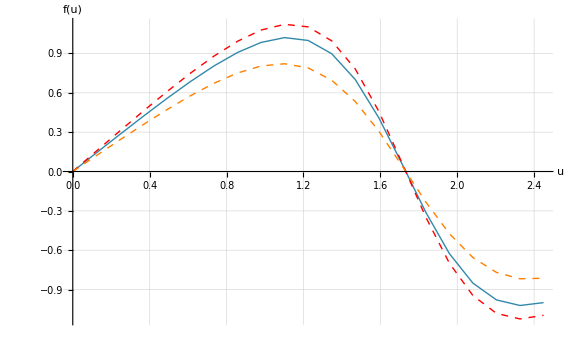

```mathematica
FrameBox["Free Energy Analysis"] // DisplayForm

FreeEnergyDataPlotAll=ListLinePlot[
{
FreeEnergyData[[1]],
FreeEnergyData[[2]],
FreeEnergyData[[3]]
},
PlotRange->All,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,RGBColor[50/255,137/255,170/255]},
{Thick,Dashed,Red},
{Thick,Dashed,Orange}
},
PlotLegend->{
Style["Harmonic",FontSize->fs3],
Style["Hard-Soft",FontSize->fs3],
Style["Soft-Hard",FontSize->fs3]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.55,0.25},
LegendPosition->{-0.7,-0.1}
]

Export["./col_fe_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",FreeEnergyDataPlotAll];

dFreeEnergyDataPlotAll=ListLinePlot[
{
dFreeEnergyData[[1]],
dFreeEnergyData[[2]],
dFreeEnergyData[[3]]
},
PlotRange->All,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["f(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,RGBColor[50/255,137/255,170/255]},
{Thick,Dashed,Red},
{Thick,Dashed,Orange}
},
PlotLegend->{
Style["Harmonic",FontSize->fs3],
Style["Hard-Soft",FontSize->fs3],
Style["Soft-Hard",FontSize->fs3]
},
LegendShadow->None,
LegendBorder->None,
LegendBackground->Opacity[0],
ShadowBackground->Opacity[0],
LegendSize->{0.55,0.25},
LegendPosition->{-0.7,-0.5}
]

Export["./col_dfe_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",dFreeEnergyDataPlotAll];
```